## Set up

### Load Paclet

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
Get["CodeGolfSEAnalysis`"]
```

### Load cleaned EntityStores

These were generated in ProcessMetadata.nb:

```mathematica
SetDirectory[NotebookDirectory[]];
codeGolfEntityStore=Import["codegolf.stackexchange.com_Cleaned_2019-10-23_11-29-19.mx"];
EntityUnregister/@codeGolfEntityStore[];
EntityRegister[codeGolfEntityStore]

SetDirectory[NotebookDirectory[]];
codeGolfLanguageEntityStore=Import["CodeGolfProgrammingLanguage_Cleaned_2019-10-23_11-29-57.mx"];
EntityUnregister/@codeGolfLanguageEntityStore[];
EntityRegister[codeGolfLanguageEntityStore]
```

{StackExchange.Codegolf:User,StackExchange.Codegolf:Badge,StackExchange.Codegolf:Comment,StackExchange.Codegolf:Post,StackExchange:PostType,StackExchange.Codegolf:Vote,StackExchange:VoteType,StackExchange.Codegolf:PostHistory,StackExchange:PostHistoryType,StackExchange:CloseReason,StackExchange.Codegolf:Tag}

{CodeGolfProgrammingLanguage}

### Helpful Definitions

```mathematica
ClearAll[NiceGrid];
NiceGrid[x_,opts___]:=Once[ResourceFunction["NiceGrid"]][Replace[x,{{}|<||>->{{}}}],opts];
```

## Language usage

### Gather all submission metadata

We’re only interested in answers, as they tend to be in a standard format and questions are prompts for which users add submissions.

```mathematica
answerToMetadata=EntityValue[
EntityClass["StackExchange.Codegolf:Post","PostType"->Entity["StackExchange:PostType","2"]],
"CodeGolfMetadata",
"EntityAssociation"
];
answerToMetadata//Length
```

142574

### Count usage per language

In reality, there really are not over 8600 programming languages used on the site -- my processing of the posts isn’t perfect since users tend to stray from the common format that is easy to parse.

```mathematica
languageToCount=ReverseSort@Counts[DeleteMissing@Values[answerToMetadata[[All,"Language"]]]];
languageToCount//Length
```

8623

In fact, the top 14 languages account for just over half of the entire site’s submissions, so in practice, there are vastly fewer real languages:

```mathematica
100*N[Total[languageToCount[[;;14]]]/Total[languageToCount]]
```

50.3277

```mathematica
languageToCount[[;;14]]
```

<|Python→13953,JavaScript→9360,Perl→5570,C→4453,Ruby→4286,Haskell→4186,Jelly→4151,Wolfram Language→4019,Java→3910,Pyth→3599,PHP→3555,05AB1E→2954,C#→2778,R→2716|>

Perhaps unsurprisingly, Python and JavaScript are the most commonly submitted languages.
However, there are many golf-specific languages that appear in the top dozen or so.

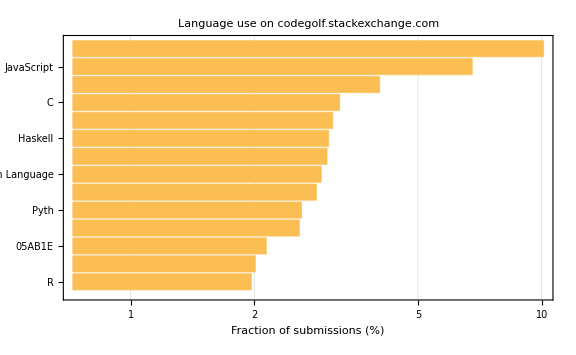

```mathematica
BarChart[100.*N[Reverse[languageToCount[[;;14]]]/Total[languageToCount]],
ScalingFunctions->"Log",
BarOrigin->Left,
ChartLabels->Automatic,
ImageSize->Large,
PlotTheme->"Detailed",
LabelStyle->18,
PlotLabel->"Language use on codegolf.stackexchange.com",
FrameLabel->{None,"Fraction of submissions (%)"}
]
```

### Languages with bad words

Several languages include bad words, and they have been somewhat “sanitized”:

```mathematica
languageToLabel=DeleteMissing@EntityValue[Keys[languageToCount],"Label","EntityAssociation"];
```

```mathematica
KeyTake[languageToCount,Keys[Select[languageToLabel,StringContainsQ[#,"\[FreakedSmiley]"]&]]][[;;12]]
```

<|Brainfu\[FreakedSmiley]\[FreakedSmiley]→820,JSFu\[FreakedSmiley]\[FreakedSmiley]→14,Boolfu\[FreakedSmiley]\[FreakedSmiley]→7,DFu\[FreakedSmiley]\[FreakedSmiley]→5,Brainfu\[FreakedSmiley]\[FreakedSmiley]𝒥 score→5,ShadyAsFu\[FreakedSmiley]\[FreakedSmiley]→4,bi\[FreakedSmiley]\[FreakedSmiley]\[FreakedSmiley]→3,Br**nfu\[FreakedSmiley]\[FreakedSmiley]→3,Wordfu\[FreakedSmiley]\[FreakedSmiley]→3,Brainfu\[FreakedSmiley]\[FreakedSmiley]𝒥 n=→3,><> → JavaScript → brainfu\[FreakedSmiley]\[FreakedSmiley] → Python→2,Eitherfu\[FreakedSmiley]\[FreakedSmiley]→2|>

## Sort Thread Submissions by Size

### Gather data

Start with a “parent” of a specific thread:

```mathematica
parent=Entity["StackExchange.Codegolf:Post","49671"];
```

Gather all of the “child” submissions:

```mathematica
submissions=EntityList@EntityClass["StackExchange.Codegolf:Post",EntityProperty["StackExchange.Codegolf:Post","ParentPost"]->parent];
submissionToMetadata=EntityValue[submissions,"CodeGolfMetadata","EntityAssociation"];
submissionToMetadata//Length
```

26

### Show

Show the submissions sorted by their reported size (a feature not available on the website without leaderboard code, which sometimes breaks):

```mathematica
NiceGrid[
{#["ReportedSize"],#["Language"],First[#["CodeSnippets"],Missing["NotFound"]]}&/@SortBy[submissionToMetadata,#ReportedSize&],
Alignment->Left
]
```

A: [Dennis] CJam, 135 134 132 130 126 125 bytes
0000000:…[»](https://codegolf.stackexchange.com/q/49722) | 125 B | CJam | 0000000: 4e22285b200a5c225f2a295c2d2e2f6f2c3e4f3a3c3d5d225f  N"([ .\"_*)\-./o,>O:<=]"_
0000019: 2422dd7382d6bfab28707190992f240c362ee510262bd07a77  $".s....(pq../$.6...&+.zw
0000032: 08556de9dcdb566c676817c2b87f5ecb8bab145dc2f2f76e07  .Um...Vlgh....^....]...n.
000004b: 22323536624b623224663d4e2f7b5f2c342f2f7d25723a7e2e  "256bKb2$f=N/{_,4//}%r:~.
0000064: 3d2828342423346222205f0a20222e2a6f6f736572372f4e2a  =((4$#4b" _. ".*ooser7/N*

A: [Kevin Cruijssen] 05AB1E, 137 135 128 bytes
…
)(ð•ž&Ž•J•£ÊÒu[7tˆ…[»](https://codegolf.stackexchange.com/q/177700) | 128 B | 05AB1E | …
)(ð•ž&Ž•J•£ÊÒu[7tˆ†ŠHλRΩ.P•12вèJsvN“_ .
\/=":><Oo-[],)*(“•æ‰ΔΣ₁çδ₂.af
r3₁’8iÈÉÞ2;lλÒžfúāÿ©-Ñm.a6Ñ`^«#„]*≠.bdÜ4~āÐm=.beç•20вè¶¡Nè4äyè.;

A: [Sp3000] CJam, 150 145 bytes
Base convert all the things!
"…[»](https://codegolf.stackexchange.com/q/49685) | 145 B | CJam | "b8li'
U9gN;|"125:Kb8bl:~f="r  pL|P3{cR`@L1iT"Kb21b"G.HMtNY7VM=BM@$^$dX8a665V"KbFb"=_./ <[(*-oO,\":"f=_"/<[(""\>])"er+4/f=.=7/N*

A: [Runer112] CJam, 164 bytes
Generates the snowman left-to-right…[»](https://codegolf.stackexchange.com/q/49682) | 164 B | CJam | q:Q;SS"
 _===_,___
 ....., _
  /_\,___
 (_*_)"',/0{Q=~(=}:G~N" \ "4G'(".oO-"_2G",._ "1G@3G')" / "5GN"< / "4G'(" : ] [> <   "3/6G')"> \ "5GNS'(" : \" \"___   "3/7G')

A: [Optimizer] CJam, 200 191 bytes
This can surely be golfed a…[»](https://codegolf.stackexchange.com/q/49679) | 191 B | CJam | 7S*"_===_  ___  .....   _    /_\   ___  (_*_)"+6/2/Nf*",._ "1/".oO-"1/_" <\  /   >/  \  "2/4/~" : ] [> <    : \" \"___   "3/4/~]l~Ab:(]z::=:L0=N4{L=}:K~0='(2K1K3K')5K0=N4K1='(6K')5K1=NS'(7K')

A: [mazzy] PowerShell, 199 bytes
Inspired by Reto Koradi and…[»](https://codegolf.stackexchange.com/q/180298) | 199 B | PowerShell for Windows | for($t='  0 _ _0 ___0 _ _
 0_. (0=./_0=._*0=.\_0_. )
4 \  (2.oO-1,._ 3.oO-)5 /  
4< / (6 ]> 6:   6 [< )5> \ 
 (7 "_ 7: _ 7 "_ )';$d=$t[$i++];$r+="$d"){if($d-ge48){$d=$t[$i+"$args"["$d"]-49]
$i+=4}}$r

A: [NinjaBearMonkey] JavaScript ES6, 210 208 202 bytes
s=>` 0
8(213)9…[»](https://codegolf.stackexchange.com/q/49720) | 202 B | JavaScript | s=>` 0
8(213)9
4(6)5
 (7)`.replace(/\d/g,p=>`_===_1 ___
 .....1  _
  /_\\1 ___
 (_*_)1,1.1_11.1o101-1.1o101-1<11/11>11\\11 : 1] [1> <1   1 : 1" "1___1   11\\11 11/11 `.split(1)[s[p>7?p-4:p]-1+p*4]||' ')

A: [Jakube] Pyth, 203 bytes
M@GCHgc"  ␣␣␣
  ␣␣␣
   ␣"bhzgc…[»](https://codegolf.stackexchange.com/q/49678) | 203 B | Pyth | M@GCHgc"  ___

  ___
   _"bhzgc" (_*_)
 _===_
 .....
  /_\\"bhzs[g"  \ "@z4\(g"-.oO"@z2g" ,._"@z1g"-.oO"@z3\)g"  / "@z5)s[g" < /"@z4\(gc"   
 : 
] [
> <"b@z6\)g" > \\"@z5)++" ("gc"   
 : 
\" \"
___"bez\)

A: [anatolyg] C, 212 bytes
d;main(){char*t="##3#b#b3#bbb3#b#b##\…[»](https://codegolf.stackexchange.com/q/49941) | 212 B | C | d;main(){char*t="##3#b#b3#bbb3#b#b##\r#3b1#+3@12b3@1b-3@1_b3b1#,#\r7#_##+51rR04/1b#61rR0,8#2##\r7?#2#+9#`A#9=###9#^?#,8A#_#\r#+:#%b#:=#b#:#%b#,#",p[9];for(gets(p);d=*t++;putchar(d-3))d=d<51?d:(p[d-51]-53)[t+=4];}

A: [Reto Koradi] C, 233 230 bytes
char*t="  0 ␣ ␣0 ␣␣␣0 ␣ ␣   0␣. (…[»](https://codegolf.stackexchange.com/q/49914) | 230 B | C | char*t="  0 _ _0 ___0 _ _   0_. (0=./_0=._*0=.\\_0_. ) 4 \\  (2.oO-1,._ 3.oO-)5 /  4< / (6 ]> 6:   6 [< )5> \\  (7 \"_ 7: _ 7 \"_ ) ";i,r,d;f(char*p){while(r++<35){d=t[i]-48;putchar(t[d<0?i:i+p[d]-48]);i+=d<0?1:5;r%7?0:puts("");}}

A: [edc65] JavaScript (ES6), 247
Not as good ad @NinjaBearMonkey…[»](https://codegolf.stackexchange.com/q/49757) | 247 B | JavaScript | 

A: [Matty] Python 3, 349 336 254 251 bytes
So much for doing…[»](https://codegolf.stackexchange.com/q/49746) | 251 B | Python | l='_===_| ___\n .....|  _\n  /_\| ___\n (_*_)| : |] [|> <|   |>| |\| | : |" "|___|   '.split('|')
l[4:4]=' \  .oO-,._ .oO- /  < / '
def s(a):print(' {}\n{}({}{}{}){}\n{}({}){}\n ({})'.format(*[l[4*m+int(a[int('0421354657'[m])])-1]for m in range(10)]))

A: [Khalil] Python 2.7, 257 bytes (i think)
H,N,L,R,X,Y,T,B=…[»](https://codegolf.stackexchange.com/q/165671) | 257 B | Python | H,N,L,R,X,Y,T,B=map(int,i)
l='\n'
s=' '
e=' .o0-'
F='  \  / '
S=' < / \ >'
o,c='()'
print s+'      _ _ ___ _ _\n\n\n\n    _. (=./_=._*=.\__. )'[H::4]+l+F[X]+o+e[L]+' ,._ '[N]+e[R]+c+F[-Y]+l+S[X]+o+'  ]> :    [< '[T::4]+c+S[-Y]+l+s+o+'  "_ : _  "_ '[B::4]+c

A: [Cees Timmerman] Python 2, 354 280 241 261 bytes
def s(g):H,N,L,R,…[»](https://codegolf.stackexchange.com/q/49683) | 261 B | Python | def s(g):H,N,L,R,X,Y,T,B=[int(c)-1for c in g];e='.oO-';print(' '*9+'_ _ ___ _ _\n\n\n\n    _. (=./_=._*=.\\__. )')[H::4]+'\n'+' \\  '[X]+'('+e[L]+',._ '[N]+e[R]+')'+' /  '[Y]+'\n'+'< / '[X]+"("+' ]> :    [< '[T::4]+')'+'> \\ '[Y]+'\n ('+' "_ : _  "_ '[B::4]+")"

A: [CL-] C, 280 272 264 bytes
Only partially golfed at this…[»](https://codegolf.stackexchange.com/q/49696) | 264 B | C | #define P(n)[s[n]&3],
f(char*s){printf("  %.3s\n %.5s\n%c(%c%c%c)%c\n%c(%.3s)%c\n (%.3s)",
"___   ___ _"+*s%4*3,"(_*_)_===_..... /_\\"+*s%4*5,"  \\ "P(4)"-.o0"P(2)    
" ,._"P(1)"-.o0"P(3)"  /"P(5)" < /"P(4)"    : ] [> <"+s[6]%4*3," > \\"P(5)
"    : \" \"___"+s[7]%4*3);}

A: [Claudiu] Python, 276 289 bytes
V='.oO-'
def F(d):
 D=lambda…[»](https://codegolf.stackexchange.com/q/49684) | 289 B | Python | V='.oO-'
def F(d):
 D=lambda i:int(d[i])-1
 print"  "+("","___"," _ ","___")[D(0)]+"\n "+\
"_. (=./_=._*=.\\__. )"[D(0)::4]+"\n"+\
" \\  "[D(4)]+"("+V[D(2)]+',._ '[D(1)]+V[D(3)]+")"+" /  "[D(5)]+'\n'+\
"< / "[D(4)]+"("+" ]> :    [< "[D(6)::4]+")"+"> \\ "[D(5)]+"\n ("+\
' "_ : _  "_ '[D(7)::4]+")"

A: [nimi] Haskell, 361 306 289 bytes
o l a b=take a$drop((…[»](https://codegolf.stackexchange.com/q/49709) | 289 B | Haskell | o l a b=take a$drop((b-1)*a)l
n="\n"
p i=id=<<["  ",o"    \n _===____ \n ..... _  \n  /_\\ ___ \n (_*_)"11a,n,o" \\  "1e,o"(.(o(O(-"2c,o",._ "1 b,o".)o)O)-)"2d,o" /  "1f,n,o"< / "1e,o"( : )(] [)(> <)(   )"5g,o"> \\ "1f,n," (",o" : )\" \")___)   )"4h]where[a,b,c,d,e,f,g,h]=map(read.(:[]))i

A: [Elcan] Dart, 307 bytes
f(i,{r='.o0-',s=' : '}){i=i.split…[»](https://codegolf.stackexchange.com/q/178178) | 307 B | Dart | f(i,{r='.o0-',s=' : '}){i=i.split('').map((j)=>int.parse(j)-1).toList();return' ${['_===_',' ___ \n.....',' /_\\ ',' ___ \n (_*_)'][i[0]]}\n${' \\  '[i[4]]}(${r[i[2]]+',._ '[i[1]]+r[i[3]]})${' /  '[i[5]]}\n${'< /  '[i[4]]}(${[s,'] [','> <','  '][i[6]]})${'> \\ '[i[5]]}\n (${[s,'" "','___','   '][i[7]]})';}

A: [Craig Roy] Haskell, 333 bytes
My first submission! Builds the…[»](https://codegolf.stackexchange.com/q/49771) | 333 B | Haskell | a=y["\n _===_\n","  ___ \n .....\n","   _  \n  /_\\ \n","  ___ \n (_*_)\n"]
d=y",._ "
c=y".oO-"
e=y"< / "
j=y" \\  "
f=y"> \\ "
k=y" /  "
y w n=w!!(n-1)
h=y[" : ","] [","> <","   "]
b=y[" ( : ) \n"," (\" \") \n"," (___) \n"," (   ) \n"]
s(m:x:o:p:n:q:t:l:_)=putStr$a m++j x:'(':c o:d n:c p:')':k q:'\n':e x:'(':h t++')':f q:'\n':b l

A: [Ciaran_McCarthy] F#, 369 bytes
let f(g:string)=
 let b=" "
 let p…[»](https://codegolf.stackexchange.com/q/160357) | 369 B | F# | let f(g:string)=
 let b=" "
 let p=printfn
 let i x=int(g.[x])-49
 p"  %s  "["";"___";" _ ";"___"].[i 0]
 p" %s "["_===_";".....";" /_\ ";"(_*_)"].[i 0]
 p"%s(%c%c%c)%s"[b;"\\";b;b].[i 4]".oO-".[i 2]",._ ".[i 1]".oO-".[i 3][b;"/";b;b;b].[i 5]
 p"%s(%s)%s"["<";b;"/";b].[i 4][" : ";"] [";"> <";"   "].[i 6][">";b;"\\";b].[i 5]
 p" (%s) "[" : ";"\" \"";"___";"   "].[i 7]

A: [Jo.] PHP, 378 bytes
'   ␣===␣␣␣␣..... ␣  /␣\ ␣␣␣(␣*␣)',…[»](https://codegolf.stackexchange.com/q/160396) | 378 B | PHP | <?$f=str_split;$r=$f($argv[1]);$p=[H=>'   _===____..... _  /_\ ___(_*_)',N=>',._ ',L=>'.oO-',R=>'.oO-',X=>' <\  /  ',Y=>' >/  \  ',T=>' : ] [> <   ',B=>' : " "___   '];echo preg_replace_callback("/[A-Z]/",function($m){global$A,$p,$r,$f;$g=$m[0];return$f($f($p[$g],strlen($p[$g])/4)[$r[array_search($g,array_keys($p))]-1])[(int)$A[$g]++];},'  HHH
 HHHHH
X(LNR)Y
X(TTT)Y
 (BBB)');

A: [M. I. Wright] TI-BASIC, 397 bytes
Important: If you want to test…[»](https://codegolf.stackexchange.com/q/49711) | 397 B | TI-Basic | Input Str9
seq(inString("1234",sub(Str9,I,1)),I,1,length(Ans→L1
"      ___   _   ___ →Str1
"_===_..... /_\ (_*_)→Str2
",._ →Str3
"•oO-→Str4
"<\/ →Str5
">/\ →Str6
" : ] [> <   →Str7
" : ¨ ¨___   →Str8
"Str1Str2Str3Str4Str5Str6Str7Str8→Str0
For(X,3,5
Output(X,2,"(   )
End
L1
Output(3,3,sub(Str4,Ans(3),1)+sub(Str3,Ans(2),1)+sub(Str4,Ans(4),1
Ans(5
Output(4-(Ans=2),1,sub(Str5,Ans,1
L1(6
Output(4-(Ans=2),7,sub(Str6,Ans,1
L1-1
For(X,1,2
Output(X+3,3,sub(expr(sub(Str0,X+6,1)),1+3Ans(X+6),3
Output(X,2,sub(expr(sub(Str0,X,1)),1+5Ans(1),5
End

A: [Kevin Cruijssen] Java 8, 548 545 432 401 399 bytes
a->{int q=50,H…[»](https://codegolf.stackexchange.com/q/125628) | 399 B | Java | a->{int q=50,H=a[0]-49,N=a[1],L=a[2],R=a[3],X=a[4],Y=a[5];return"".format(" %s%n %s%n%c(%c%c%c)%c%n%c(%s)%c%n (%s)",H<1?"":H%2<1?" ___":"  _","_===_s.....s /_\\s(_*_)".split("s")[H],X==q?92:32,L<q?46:L<51?111:L<52?79:45,N<q?44:N<51?46:N<52?95:32,R<q?46:R<51?111:R<52?79:45,Y==q?47:32,X<q?60:X%2<1?32:47,"   s : s] [s> <".split("s")[a[6]%4],92-(Y%3+Y%6/4)*30,"   s : s\" \"s___".split("s")[a[7]%4]);}

A: [OganM] R 414 Bytes
Slightly modified version of Molx's…[»](https://codegolf.stackexchange.com/q/49780) | 414 B | R | W =c("_===_"," ___\n .....","  _\n  /_\\"," ___\n (_*_)",",",".","_"," ",".","o","O","-"," ","\\"," "," ","<"," ","/"," "," ","/"," ","",">"," ","\\",""," : ","] [","> <","   "," : ","\" \"","___","   ")
f=function(x){i=as.integer(strsplit(x,"")[[1]]);cat(" ",W[i[1]],"\n",W[i[5]+12],"(",W[i[3]+8],W[i[2]+4],W[i[4]+8],")",W[i[6]+20],"\n",W[i[5]+16],"(",W[i[7]+28],")",W[i[6]+24],"\n"," (",W[i[8]+32], ")",sep="")}

A: [Molx] R, 436 437 bytes
Here's my first try on code-golf…[»](https://codegolf.stackexchange.com/q/49692) | 437 B | R | H=c("_===_"," ___\n .....","  _\n  /_\\"," ___\n (_*_)")
N=c(",",".","_"," ")
L=c(".","o","O","-")
X=c(" ","\\"," "," ")
S=c("<"," ","/"," ")
Y=c(" ","/"," ","")
U=c(">"," ","\\","")
T=c(" : ","] [","> <","   ")
B=c(" : ","\" \"","___","   ")
f=function(x){i=as.integer(strsplit(x,"")[[1]]);cat(" ",H[i[1]],"\n",X[i[5]],"(",L[i[3]],N[i[2]],L[i[4]],")",Y[i[6]],"\n",S[i[5]],"(",T[i[7]],")",U[i[6]],"\n"," (",B[i[8]], ")",sep="")}

A: [Christopher Reid] JavaScript, 489 (without newlines and tabs)
x=' ';…[»](https://codegolf.stackexchange.com/q/49674) | 489 B | JavaScript | x=' ';
d="   ";
h=['\n_===_',' ___ \n.....','  _  \n /_\\ ',' ___ \n(_*-)'];
n=[',','.','_',x];
e=['.','o','O','-'];
y=['>',,'\\',x];
u=['<',,'/',x];
t=[' : ','[ ]','> <',d;
b=[' : ','" "',"___",d];

j=process.argv[2].split('').map(function(k){return parseInt(k)-1});
q=j[4]==1;
w=j[5]==1;

console.log([
    h[j[0]].replace(/(.*)\n(.*)/g, " $1\n $2"),
    (q?'\\':x)+'('+e[j[2]]+n[j[1]]+e[j[3]]+')'+(w?'/':x),
    (!q?u[j[4]]:x)+'('+t[j[6]]+')'+(!w?y[j[5]]:x),
    x+'('+b[j[7]]+')'].join('\n'));

## Evaluate submissions in Notebooks

#### Python example

Look at a specific python submission:

```mathematica
Entity["StackExchange.Codegolf:Post","49746"]["SubmissionCodeSnippets"]
```

{l='_===_| ___\n .....|  _\n  /_\| ___\n (_*_)| : |] [|> <|   |>| |\| | : |" "|___|   '.split('|')
l[4:4]=' \  .oO-,._ .oO- /  < / '
def s(a):print(' {}\n{}({}{}{}){}\n{}({}){}\n ({})'.format(*[l[4*m+int(a[int('0421354657'[m])])-1]for m in range(10)]))
}

Evaluating it directly in a notebook just requires some easy setup:

l='_===_| ___\n .....|  _\n  /_\| ___\n (_*_)| : |] [|> <|   |>| |\| | : |" "|___|   '.split('|')
l[4:4]=' \  .oO-,._ .oO- /  < / '
def s(a):print(' {}\n{}({}{}{}){}\n{}({}){}\n ({})'.format(*[l[4*m+int(a[int('0421354657'[m])])-1]for m in range(10)]))

s('11112311')

_===_

\(.,.)

( : )\

( : )

#### Node.js example

Look at a specific Node.js submission:

```mathematica
Entity["StackExchange.Codegolf:Post","49674"]["SubmissionCodeSnippets"]
```

{x=' ';
d="   ";
h=['\n_===_',' ___ \n.....','  _  \n /_\\ ',' ___ \n(_*-)'];
n=[',','.','_',x];
e=['.','o','O','-'];
y=['>',,'\\',x];
u=['<',,'/',x];
t=[' : ','[ ]','> <',d;
b=[' : ','" "',"___",d];

j=process.argv[2].split('').map(function(k){return parseInt(k)-1});
q=j[4]==1;
w=j[5]==1;

console.log([
    h[j[0]].replace(/(.*)\n(.*)/g, " $1\n $2"),
    (q?'\\':x)+'('+e[j[2]]+n[j[1]]+e[j[3]]+')'+(w?'/':x),
    (!q?u[j[4]]:x)+'('+t[j[6]]+')'+(!w?y[j[5]]:x),
    x+'('+b[j[7]]+')'].join('\n'));
}

Evaluating this in a notebook also requires some easy setup.
This particular submission requires some other changes to get it to work with regard to argument handling:

```mathematica
ExternalEvaluate["NodeJS",
"
// Use my own variable instead of process.argv[2]
arg='33232124';

x=' ';
d=\"   \";
h=['\\n_===_',' ___ \\n.....','  _  \\n /_\\\\ ',' ___ \\n(_*-)'];
n=[',','.','_',x];
e=['.','o','O','-'];
y=['>',,'\\\\',x];
u=['<',,'/',x];
t=[' : ','[ ]','> <',d]; // Fixed a small typo here
b=[' : ','\" \"',\"___\",d];

// arg used to be process.argv[2] here
j=arg.split('').map(function(k){return parseInt(k)-1});
q=j[4]==1;
w=j[5]==1;

[
    h[j[0]].replace(/(.*)\\n(.*)/g, \" $1\\n $2\"),
    (q?'\\\\':x)+'('+e[j[2]]+n[j[1]]+e[j[3]]+')'+(w?'/':x),
    (!q?u[j[4]]:x)+'('+t[j[6]]+')'+(!w?y[j[5]]:x),
    x+'('+b[j[7]]+')'].join('\\n')"
]
```

_  
  /_\ 
\(o_O) 
 ([ ])>
 (   )

## Gather Top Languages by post tags

### Definition

For a given tag, gather the metadata for all submissions (answers) with that tag.
Then, find the ten most commonly submitted languages.

```mathematica
ClearAll[tagToLanguageBreakdown];
tagToLanguageBreakdown[tagConstraint_]:=With[
{
postToTagMetadata=EntityValue[
EntityClass["StackExchange.Codegolf:Post",{"Tags"->tagConstraint,"PostType"->Entity["StackExchange:PostType","2"]}],
"CodeGolfMetadata",
"EntityAssociation"
]
},
Take[ReverseSort@Counts[Lookup[Values[postToTagMetadata],"Language"]],UpTo[10]]
];
```

### Examples

Unsurprisingly, submissions for posts with math-related tags use Wolfram Language quite a bit:

```mathematica
tagToLanguageBreakdown[Entity["StackExchange.Codegolf:Tag","primes"]]
```

<|Python→347,Jelly→209,Wolfram Language→188,JavaScript→179,Pyth→155,Perl→141,05AB1E→129,Haskell→129,Ruby→113,Java→94|>

```mathematica
tagToLanguageBreakdown[Entity["StackExchange.Codegolf:Tag","math"]]
```

<|Python→1726,JavaScript→1020,Wolfram Language→770,Haskell→702,Jelly→687,Perl→664,Pyth→553,C→537,Ruby→464,APL→435|>

```mathematica
tagToLanguageBreakdown[Entity["StackExchange.Codegolf:Tag","number"]]
```

<|Python→1844,JavaScript→1168,Perl→790,Jelly→789,Wolfram Language→711,Haskell→701,Pyth→629,05AB1E→577,Java→573,C→533|>

```mathematica
tagToLanguageBreakdown[Entity["StackExchange.Codegolf:Tag","sequence"]]
```

<|Python→1126,JavaScript→641,Jelly→527,Haskell→475,Wolfram Language→458,Perl→430,Pyth→397,05AB1E→372,Java→292,Ruby→286|>

Other submission categories don’t use Wolfram Language as much:

```mathematica
tagToLanguageBreakdown[Entity["StackExchange.Codegolf:Tag","ascii-art"]]
```

<|Python→1543,JavaScript→1020,Perl→531,C→529,Ruby→460,PHP→392,Java→342,Haskell→326,Pyth→325,05AB1E→315|>

```mathematica
tagToLanguageBreakdown[Entity["StackExchange.Codegolf:Tag","string"]]
```

<|Python→2718,JavaScript→2020,Perl→1359,C→952,Ruby→904,PHP→883,Pyth→862,Java→840,Jelly→828,Haskell→788|>

```mathematica
tagToLanguageBreakdown[Entity["StackExchange.Codegolf:Tag","quine"]]
```

<|Python→187,JavaScript→163,CJam→100,Perl→76,Ruby→63,Java→58,Haskell→55,C→50,><> Fish→46,Jelly→43|>

## Language Ranks per thread with symbolic SPARQL queries

### Gather thread language data

Write a symbolic SPARQL query to extract languages used and their reported submission sizes for a given thread (i.e. “parent post”).

```mathematica
Needs["GraphStore`"]
threadLanguageData=Entity["StackExchange.Codegolf:Post"]//SPARQLSelect[
{
RDFTriple[SPARQLVariable["parentPost"],EntityProperty["StackExchange.Codegolf:Post","PostType"],Entity["StackExchange:PostType","1"]],
RDFTriple[SPARQLVariable["submission"],EntityProperty["StackExchange.Codegolf:Post","ParentPost"],SPARQLVariable["parentPost"]],
RDFTriple[SPARQLVariable["submission"],EntityProperty["StackExchange.Codegolf:Post","SubmissionReportedSize"],SPARQLVariable["reportedSize"]],
RDFTriple[SPARQLVariable["submission"],EntityProperty["StackExchange.Codegolf:Post","SubmissionProgrammingLanguage"],SPARQLVariable["language"]]
}->{"parentPost","language","reportedSize","submission"}
];//AbsoluteTiming
```

{24.3875,Null}

```mathematica
threadLanguageData[[;;1]]
```

{<|parentPost→Q: [MiffTheFox] ROT-13 transform standard input[»](https://codegolf.stackexchange.com/q/4),language→Bash,reportedSize→23 B,submission→A: [Chris Jester-Young] Bash, 23 bytes
Canonical 23-character answer:
tr…[»](https://codegolf.stackexchange.com/q/6)|>}

Group the results by thread and language, sorting by reported size.
Note that different units are treated the same here since it’s difficult to compare different units (e.g. bytes vs keystrokes vs characters in different encodings, etc...).

```mathematica
threadToSubmissionLanguageBreakdown=GroupBy[threadLanguageData,Key["parentPost"],GroupBy[Key["language"]->Key["reportedSize"]]/*SortBy[QuantityMagnitude/*Min]];
```

```mathematica
threadToSubmissionLanguageBreakdown[[;;1]]
```

<|Q: [MiffTheFox] ROT-13 transform standard input[»](https://codegolf.stackexchange.com/q/4)→<|CHIQRSX→{1 B},Bash→{23 B,5 characters},vim→{5 keystrokes},05AB1E→{12 B},Jelly→{13 B},Retina→{13 B},8086 machine→{27 B},PHP→{41 characters,80 characters,27 B},Japt→{28 B},J→{29 B},K→{31 B},Python→{34 B,117 B,107 B,60 B,70 B},R→{37 B},Ruby→{37 characters},zsh→{56 B},Befunge→{156 characters,123 B,67 B},C→{79 characters,68 characters,136 B},Julia→{69 B},Tcl→{74 characters},pyg𝒥i→{76 B},PowerShell for Windows→{77 B},C#→{94 B},Scala→{108 B,96 characters},Haskell→{112 characters,100 characters,103 B},Wolfram Language→{102 B},JavaScript→{177 B,106 B,165 B,135 B},DC→{108 B},Delphi→{110 B},///→{217 B},Java→{251 characters},LispLisp→{16636 B}|>|>

Here are some helpful definitions for getting position ranks with ties:

```mathematica
ClearAll[RankWithTies];
RankWithTies[keyToScore_Association,key_,ordering_:OrderedQ]:=First@RankWithTies[keyToScore,{key},ordering];
RankWithTies[keyToScore_Association,keys_List,ordering_:OrderedQ]:=With[
{keyRankStructure=Values@Sort[GroupBy[keyToScore,Identity,Keys],ordering]},
AssociationMap[
First[
Position[keyRankStructure,#][[All,1]],
Missing["NotFound"]
]&,
keys
]
];
RankWithTies[<|"A"->1,"B"->2,"C"->2,"D"->3,"D"->3|>,"C"]
```

2

```mathematica
ClearAll[RankWithTiesBy];
RankWithTiesBy[keyToScore_Association,key_,orderingBy_:Identity]:=First@RankWithTiesBy[keyToScore,{key},orderingBy];
RankWithTiesBy[keyToScore_Association,keys_List,orderingBy_:Identity]:=With[
{keyRankStructure=Values@KeySort[GroupBy[keyToScore,orderingBy,Keys]]},
AssociationMap[
First[
Position[keyRankStructure,#][[All,1]],
Missing["NotFound"]
]&,
keys
]
];
RankWithTiesBy[<|"A"->1,"B"->2,"C"->2,"D"->3,"D"->3|>,"C"]
```

2

Look at the rank stats across all threads for some common languages:

```mathematica
languageToRanks=AssociationMap[
Function[
language,
DeleteMissing[RankWithTiesBy[#,language,QuantityMagnitude/*Min]&/@threadToSubmissionLanguageBreakdown]
],
{Entity["CodeGolfProgrammingLanguage","Python::4g426"],Entity["CodeGolfProgrammingLanguage","JavaScript::g3427"],Entity["CodeGolfProgrammingLanguage","WolframLanguage"],Entity["CodeGolfProgrammingLanguage","C::5zm8v"],Entity["CodeGolfProgrammingLanguage","C::y7pg6"],Entity["CodeGolfProgrammingLanguage","Rust::8y9w4"],Entity["CodeGolfProgrammingLanguage","Go::3m7v3"]}
];
```

On average, Wolfram Language is not all that different in ranking compared to the most popular languages.
Lower-level and compiled languages tend to do worse in code golf, likely due to their requirement for boilerplate code (e.g. strong/static typing).

```mathematica
NiceGrid[
Function[
ranks,
AssociationMap[N[Replace[#[ranks],Except[_?NumericQ]->Missing[]]]&,{Length,Min,Median,Mean,Max}]
]/@languageToRanks
]
```

| Length | Min | Median | Mean | Max
Python | 6902. | 1. | 6. | 6.93437 | 58.
JavaScript | 5592. | 1. | 6. | 7.43366 | 45.
Wolfram Language | 3163. | 1. | 6. | 7.22163 | 79.
C# | 1897. | 1. | 13. | 14.4212 | 116.
C++ | 777. | 1. | 15. | 15.8018 | 66.
Rust | 190. | 2. | 20. | 21.6053 | 153.
Go | 166. | 1. | 22. | 24.5542 | 143.

Find the most common languages in first place (not considering ties for simplicity):

```mathematica
firstPlaceLanguageToCount=ReverseSort@Counts[Select[Values[Keys/@threadToSubmissionLanguageBreakdown],Length[#]≥1&][[All,1]]];
firstPlaceLanguageToCount//Length
```

918

Wolfram Language takes first place (without ties) the 9th most often among all threads:

```mathematica
firstPlaceLanguageToCount[[;;12]]
```

<|Jelly→1437,05AB1E→869,Python→723,Pyth→680,CJam→481,JavaScript→389,Perl→327,APL→303,Wolfram Language→258,Golfscript→237,MATL→225,Ruby→213|>

Find the parent posts of the winning Wolfram Language submissions:

```mathematica
parentPostsWithWLWinners=Keys@Select[threadToSubmissionLanguageBreakdown,RankWithTiesBy[#,Entity["CodeGolfProgrammingLanguage","WolframLanguage"],QuantityMagnitude/*Min]===1&];
parentPostsWithWLWinners//Length
```

274

```mathematica
parentPostsWithWLWinners[[;;3]]
```

{Q: [fR0DDY] Partition of a positive integer N[»](https://codegolf.stackexchange.com/q/812),Q: [Dan McGrath] Rand5() to Rand7()[»](https://codegolf.stackexchange.com/q/13),Q: [JiminP] Solve the knapsack problem[»](https://codegolf.stackexchange.com/q/3731)}

Write another symbolic SPARQL query to extract out the actual Wolfram Language submission posts:

```mathematica
wlWinningSubmissions=Entity["StackExchange.Codegolf:Post"]//SPARQLSelect[
{
SPARQLValues["parentPost",parentPostsWithWLWinners],
RDFTriple[SPARQLVariable["submission"],EntityProperty["StackExchange.Codegolf:Post","ParentPost"],SPARQLVariable["parentPost"]],
RDFTriple[SPARQLVariable["submission"],EntityProperty["StackExchange.Codegolf:Post","SubmissionProgrammingLanguage"],Entity["CodeGolfProgrammingLanguage","WolframLanguage"]]
}->"submission"
]//Lookup["submission"];//AbsoluteTiming
```

{8.22541,Null}

Look at the smallest such winners. Note the  heavy use of built-ins and infix forms.

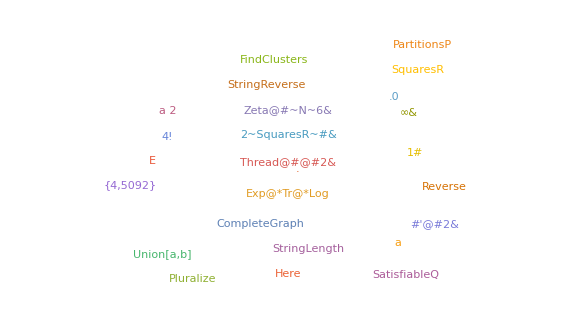

```mathematica
postToWinningWLSnippet=First[#,Missing["NotFound"]]&/@EntityValue[wlWinningSubmissions,"SubmissionCodeSnippets","EntityAssociation"];
WordCloud[
KeyValueMap[Tooltip[Button[#2,Paste[#1],Appearance->"Frameless"],#1["URL"]]&,TakeSmallestBy[StringTrim/@Select[postToWinningWLSnippet,MatchQ[_String]],StringLength,25]],
ImageSize->Large,
WordSpacings->5,
AspectRatio->9/16
]
```

Perhaps unsurprisingly, the most common symbolic (non-alphanumeric) characters are @ (for common infix notations), square brackets, and pure function notation (all staples of Wolfram Language one-liner submissions).

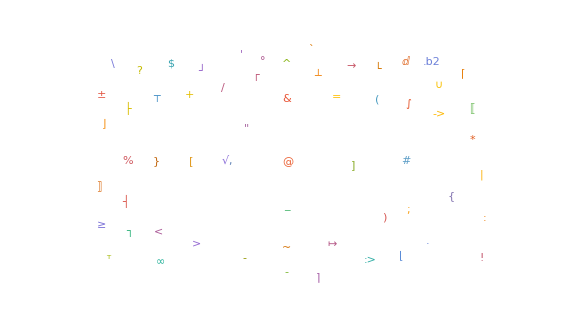

```mathematica
WordCloud[
KeySelect[StringMatchQ[LetterCharacter|DigitCharacter]/*Not]@ReverseSort@Counts@Flatten@Characters@StringTrim@Cases[Values[postToWinningWLSnippet],_String],
AspectRatio->9/16,
WordSpacings->3,
ImageSize->Large
]
```

Extracting out the actual expressions can let us see which actual symbols are the most common:

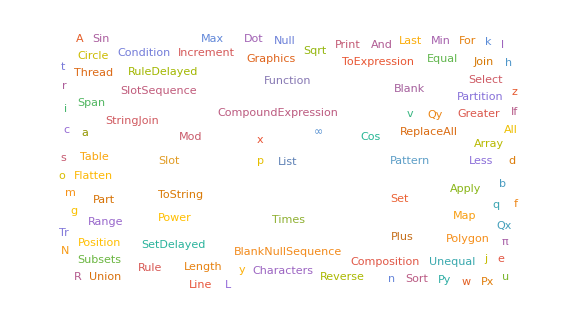

```mathematica
winningExpressions=Cases[Values[postToWinningWLSnippet],s_String:>Quiet@ToExpression[s,StandardForm,HoldComplete],Infinity];
WordCloud[
ReverseSort@Counts[Extract[#,Position[#,_Symbol,{3,Infinity},Heads->True],HoldForm]&[winningExpressions]],
WordSpacings->3,
ImageSize->Large,
AspectRatio->9/16
]
```

The most common letter is e, which is also the most common letter in typical English.
This is likely because most built-in symbols have English-similar names.

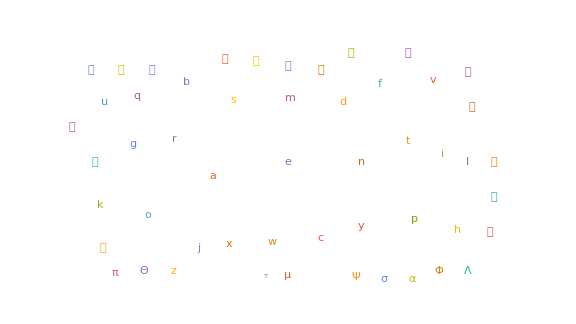

```mathematica
WordCloud[
KeySelect[StringMatchQ[LetterCharacter]]@ReverseSort@Counts@Flatten@Characters@StringTrim@Cases[Values[postToWinningWLSnippet],_String],
AspectRatio->9/16,
WordSpacings->3,
ImageSize->Large
]
```

## User language use time series

### Gather Data

Use a symbolic SPARQL query to extract when users use which languages for submissions:

```mathematica
Needs["GraphStore`"]
userLanguageData=Entity["StackExchange.Codegolf:Post"]//SPARQLSelect[
{
RDFTriple[SPARQLVariable["submission"],EntityProperty["StackExchange.Codegolf:Post","PostType"],Entity["StackExchange:PostType","2"]],
RDFTriple[SPARQLVariable["submission"],EntityProperty["StackExchange.Codegolf:Post","Owner"],SPARQLVariable["user"]],
RDFTriple[SPARQLVariable["submission"],EntityProperty["StackExchange.Codegolf:Post","CreationDate"],SPARQLVariable["creationDate"]],
RDFTriple[SPARQLVariable["submission"],EntityProperty["StackExchange.Codegolf:Post","SubmissionProgrammingLanguage"],SPARQLVariable["language"]]
}->{"user","creationDate","language"}
];//AbsoluteTiming
userLanguageData//Length
```

{23.6961,Null}

137074

### Submission Dates/times

```mathematica
dates=DeleteMissing@userLanguageData[[All,"creationDate"]];
dates//Length
```

137074

It seems that most users on codegolf.stackexchange.com may be students, as they submit more often in the summer months and during the week. Also, noon appears to be the most common submission time, shortly followed by 5pm-6pm.

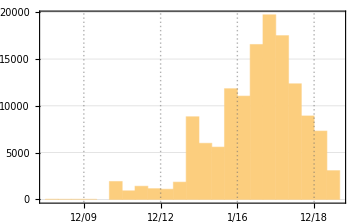
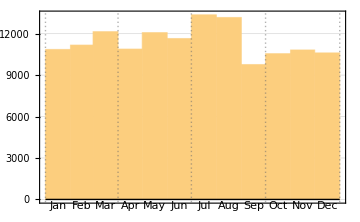
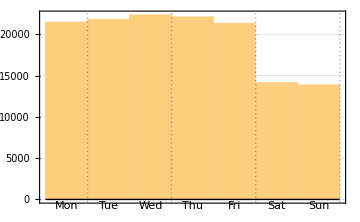
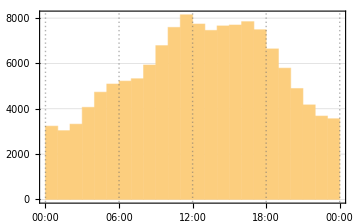

```mathematica
DateHistogram[dates,PlotTheme->"Detailed",DateReduction->#,ImageSize->Medium]&/@{None,"Year","Week","Day"}
```

Pair the day of week with the submission hour:

```mathematica
dayOfWeekToHourCounts=GroupBy[dates,DateString[#,"DayNameShort"]&,GroupBy[DateString[#,"Hour24"]&]/*Map[Length]];//AbsoluteTiming
```

{195.896,Null}

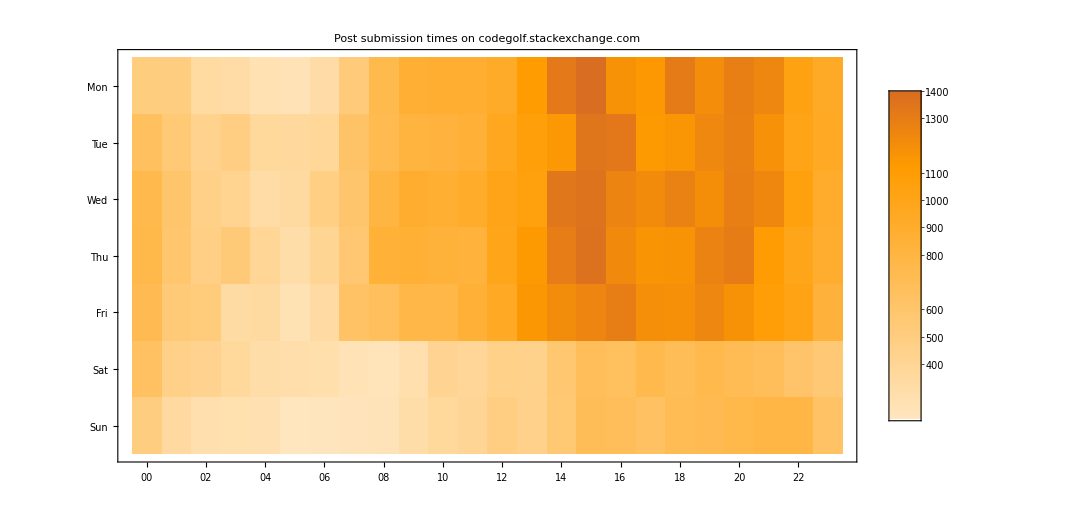

```mathematica
allHourNumberStrings=StringPadLeft[ToString[#],2,"0"]&/@Range[0,23];
allDayOfWeekStrings={"Mon","Tue","Wed","Thu","Fri","Sat","Sun"};
matrixData=KeyTake[KeyTake[allHourNumberStrings]/@dayOfWeekToHourCounts,allDayOfWeekStrings];
MatrixPlot[
Values/@Values[matrixData],
ImageSize->900,
FrameTicks->{
MapIndexed[{#2[[1]],#1}&,allDayOfWeekStrings],
MapIndexed[{#2[[1]],#1}&,allHourNumberStrings]
},
PlotTheme->{"Web","BoldLabels"},
LabelStyle->18,
PlotLabel->"Post submission times on codegolf.stackexchange.com",
PlotLegends->Placed[Automatic,After],
AspectRatio->9/16
]
```

### Languages per user

```mathematica
userToLanguageUseTimeSeries=GroupBy[userLanguageData,Key["user"]->Lookup[{"creationDate","language"}],SortBy[First]];
```

Most users only ever make submissions in one language, though several users use many dozens of different languages:

1

2.77033

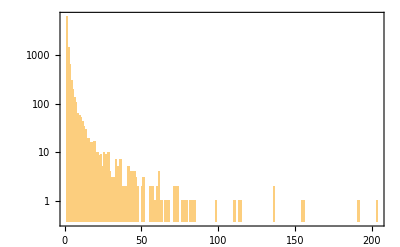

```mathematica
userToLanguageCount=DeleteDuplicates/*Length/@userToLanguageUseTimeSeries[[All,All,2]];
Values[userToLanguageCount]//Median
Values[userToLanguageCount]//Mean//N
Histogram[Values[userToLanguageCount],Automatic,{"Log","Count"},PlotTheme->"Detailed",ImageSize->Automatic,PlotRange->All]
```

### Top User language use

These are the users with the most unique language submissions:

```mathematica
TakeLargest[userToLanguageCount,5]
```

<|Dennis[»](https://codegolf.stackexchange.com/users/12012)→203,Martin Ender[»](https://codegolf.stackexchange.com/users/8478)→191,Lynn[»](https://codegolf.stackexchange.com/users/3852)→155,Conor O'Brien[»](https://codegolf.stackexchange.com/users/31957)→154,jimmy23013[»](https://codegolf.stackexchange.com/users/25180)→136|>

```mathematica
ClearAll[datelabel];
datelabel[{start_,end_},pos_,label_]:=Row[DateString[#,{"MonthName"," ","Day"}]&/@{start,end}," ~ "];

ClearAll[programmingLanguageTimelinePlot];
Options[programmingLanguageTimelinePlot]=Options[TimelinePlot];
programmingLanguageTimelinePlot[languageTimeSeries:{{_DateObject,_}...},opts:OptionsPattern[]]:=Module[
{groupedLanguageTimelines,timelinePlot},
groupedLanguageTimelines=GroupBy[
languageTimeSeries,
Last->First/*(DayRound[#,All,"Preceding"]&),
RightComposition[
DeleteDuplicates,
Split[#,DateDifference[##]<=Quantity[1,"Days"]&]&,
Map[MinMax/*Replace[{a_,b_}:>{a,b+Quantity[1,"Days"]}]/*Interval]
]
];
timelinePlot=TimelinePlot[
Values[groupedLanguageTimelines],
(*Filling->Below,*)
PlotTheme->"Detailed",
PlotLayout->"Overlapped",
LabelingFunction->datelabel,
opts
];
Show[
timelinePlot,
Frame->{{True,True},{True,True}},
Options[timelinePlot,FrameTicks]/.{None,None}->{MapIndexed[{#2[[1]],#}&,Keys[groupedLanguageTimelines]],None}
]

];
```

The user with the most languages seems to have taken a hiatus around the start of 2019, but focused on many golf-specific languages:

```mathematica
programmingLanguageTimelinePlot[userToLanguageUseTimeSeries[Entity["StackExchange.Codegolf:User","12012"]]/.Except[Alternatives[Entity["CodeGolfProgrammingLanguage","jelly"],Entity["CodeGolfProgrammingLanguage","cjam"],Entity["CodeGolfProgrammingLanguage","Python::4g426"],Entity["CodeGolfProgrammingLanguage","Julia::p5sm4"],Entity["CodeGolfProgrammingLanguage","golfscript"]],_Entity]:>"Other",AspectRatio->1/2,LabelStyle->18,PlotLabel->Entity["StackExchange.Codegolf:User","12012"]]
```

-Graphics-

The user with the second most unique languages appears to be quite fluent in Wolfram Language, and also somewhat recently took a hiatus.

```mathematica
programmingLanguageTimelinePlot[userToLanguageUseTimeSeries[Entity["StackExchange.Codegolf:User","8478"]]/.Except[Alternatives[Entity["CodeGolfProgrammingLanguage","cjam"],Entity["CodeGolfProgrammingLanguage","retina"],Entity["CodeGolfProgrammingLanguage","WolframLanguage"],Entity["CodeGolfProgrammingLanguage","alice"],Entity["CodeGolfProgrammingLanguage","labyrinth"],Entity["CodeGolfProgrammingLanguage","Ruby::f23v5"]],_Entity]:>"Other",AspectRatio->1/2,LabelStyle->18,PlotLabel->Entity["StackExchange.Codegolf:User","8478"]]
```

-Graphics-

## Machine Learning Code Golf Programming Language Classifier

### Gather First snippets

First snippets are almost always the submission code.

```mathematica
languageToFirstSnippets0=GroupBy[Values[answerToMetadata],Lookup["Language"]->Lookup["CodeSnippets"]/*(First[#,Missing["NotFound"]]&),Cases[_String]]//KeyDrop[{Missing["KeyAbsent","Language"],Missing["NotFound"]}]//ReverseSortBy[Length];
languageToFirstSnippets0//Length
```

8623

Trim down to a smaller set of languages with enough training data:

```mathematica
languageToFirstSnippets=Select[languageToFirstSnippets0,Length/*GreaterEqualThan[1000]];
languageToFirstSnippets//Length
languageToFirstSnippets//Map[Length]//Total
Length/@languageToFirstSnippets
```

26

89855

<|Python→13948,JavaScript→9348,Perl→5496,C→4447,Ruby→4285,Haskell→4186,Jelly→4148,Wolfram Language→4018,Java→3905,Pyth→3597,PHP→3553,05AB1E→2954,C#→2776,R→2712,CJam→2627,APL→2559,J→2086,PowerShell for Windows→1824,Octave𝒥 score→1782,Japt→1774,MATL→1766,Retina→1604,Bash→1162,C++→1124,Golfscript→1106,Julia→1068|>

### Separate into training and testing sets

```mathematica
With[
{languageToSplitData=TakeDrop[RandomSample[Cases[#,_String]],Floor[0.75*Length[#]]]&/@languageToFirstSnippets},
trainingData=languageToSplitData[[All,1]];
testingData=languageToSplitData[[All,2]];
]
```

```mathematica
Total[Length/@trainingData]
```

67383

### Train Classifier

```mathematica
c=Classify[trainingData,PerformanceGoal->"Quality",FeatureTypes->"Text"];//AbsoluteTiming
```

{200.272,Null}

### Test and measure accuracy

```mathematica
c/@testingData[[;;5,1]]
```

<|Python→Python,JavaScript→JavaScript,Perl→Perl,C→C,Ruby→Perl|>

```mathematica
cm=ClassifierMeasurements[c,testingData]
```

ClassifierMeasurementsObject[…]

About 87% accuracy is quite good:

```mathematica
cm["Accuracy"]
```

0.869616

```mathematica
NiceGrid[c[#,"TopProbabilities"]&/@testingData[[;;6,1]]]
```

Python | Python→1. |  | 
JavaScript | JavaScript→1. |  | 
Perl | Perl→0.999999 |  | 
C | C→1. |  | 
Ruby | Perl→0.518692 | Ruby→0.363849 | Bash→0.11724
Haskell | Haskell→1. |  |

### Attempt to classify unclassified submissions

There aren’t too many submissions without languages, but there are some:

```mathematica
answerToUnclassifiedSubmissions=Select[answerToMetadata,MatchQ[{Lookup[#,"Language"],Replace[Lookup[#,"CodeSnippets"],{{x_,___}:>x,_->Missing[]}]},{_Missing,_String}]&];
answerToUnclassifiedSubmissions//Length
```

3181

Use the newly-trained classifier to try to fill in the gaps:

```mathematica
answerToReclassifiedSubmissions=Join[#,<|"Language"->c[First[Lookup[#,"CodeSnippets"]]],"Classified"->True|>]&/@answerToUnclassifiedSubmissions;//AbsoluteTiming
```

{25.5194,Null}

The results are decent, but need some manual cleaning up to be more accurate:

```mathematica
NiceGrid[{#Language,Snippet[First[#CodeSnippets],10]}&/@answerToReclassifiedSubmissions[[;;5]],Alignment->Left]
```

A: [Daniel Standage] Definitely doesn't qualify as creative, but it gets…[»](https://codegolf.stackexchange.com/q/5) | R | perl -e '$i=99;while($i>1){print("$i bottles of beer on the wall, $i bottles of
beer.\nTake one down and pass it around, ".--$i." bottles of beer on the
wall\n\n");}print("1 bottle of beer on the wall, 1 bottle of beer.\nGo to the
store and buy some more, 99 bottles of beer on the wall.\n");'
A: [Anon.] tr/// solution in Perl (39 characters), boilerplate…[»](https://codegolf.stackexchange.com/q/12) | Perl | while(<>){y/a-zA-Z/n-za-mN-ZA-M/;print}
A: [Rob White] Who said C# had too much ceremony? Whoever it was…[»](https://codegolf.stackexchange.com/q/15) | C# | using System;
using System.Collections.Generic;
using System.Linq;
using System.Text;

namespace _99Bottles
{
    class Program
    {
        static void Main(string[] args)
A: [Dan McGrath] In c/c++ using rejection sampling
int rand7(){int…[»](https://codegolf.stackexchange.com/q/19) | Java | int rand7(){int x=8;while(x>7)x=rand5()+5*rand5()-5;return x;}
A: [Alexandru] In Python:
def Rand7():
  while True:
    x = (…[»](https://codegolf.stackexchange.com/q/21) | Python | def Rand7():
  while True:
    x = (Rand5() - 1) * 5 + (Rand5() - 1)
    if x < 21: return x/3 + 1

At this stage, I could update the metadata and re-export the EntityStores, but for now, this is a good stopping point.